```mathematica
ClearAll[TInt,Thelper,soln,solnSymm,ssiSolns,ssiSpinodalTemps]
```

```mathematica
ϵ[ξ_]:=3/2(ξ(√(ξ+1)-1))^(1/3)((ξ/(√(ξ+1)-1)^2)^(1/3)-1);
```

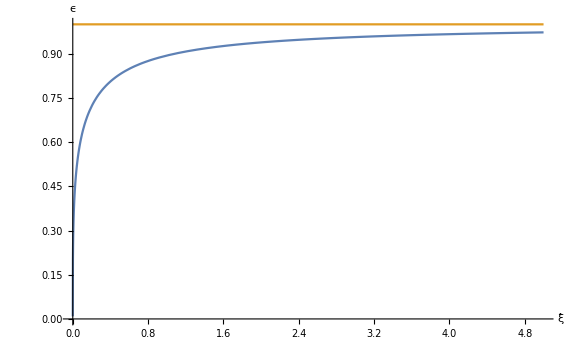

```mathematica
zeroModeEpsPlot=Plot[{ϵ[ξ],1},{ξ,0,5},PlotRange->{{0,5},{0,1}},ImageSize->Large,AxesLabel->{ξ̂,ϵ},LabelStyle->Larger]
```

```mathematica
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch5", "zero_mode_epsilon.eps"}],zeroModeEpsPlot]
```

C:\Users\Michael\Dropbox\PhD-thesis\images\ch5\zero_mode_epsilon.eps

```mathematica
TInt[0,b_]:=1/(12 b^2);
TInt[a_,∞]:=0;
TInt[a_/;a<0,b_]:=0;
AbsoluteTiming[Thelper=ListInterpolation[ParallelTable[1/(2 π^2)NIntegrate[u^2/(√(u^2+a)(Exp[b √(u^2+a)]-1)),{u,0,∞}],{a,0,4,0.01},{b,0.01,10,0.01}],{{0,4},{0.01,10}}];]
TInt[a_/;4≥a≥0,b_/;10≥b≥0.01]:=Thelper[a,b];
TInt[a_,b_]:=1/(2 π^2)NIntegrate[u^2/(√(u^2+a)(Exp[b √(u^2+a)]-1)),{u,0,∞}];
```

{277.26,Null}

```mathematica
soln[λ_,n_,Xb_,∞,β_:∞,tol_:10^-10,updateWeight_:0.25,maxIters_:1000,startPoint_:{3,1,1}]:=Module[{w=updateWeight,iterrhs},
iterrhs[{x_,y_,zz_}]:=N[((1-w){x,y,z}+w{Xb-(n-1)(1/(16 π^2)y Log[y]+TInt[y,β])-3(1/(16 π^2)z Log[z]+TInt[N@((λ x)/3),β]),
λ/6(x-Xb)+(n+1)/6 λ(1/(16 π^2)y Log[y]+TInt[y,β])+λ/6(1/(16 π^2)z Log[z]+TInt[N@((λ x)/3),β]),z})/.z->((λ x)/3)//Evaluate];
FixedPoint[iterrhs,startPoint,maxIters,SameTest->(Norm[#1-#2]<tol&)]
];
soln[λ_,n_,Xb_,ζ_/;0<ζ<∞,β_:∞,tol_:10^-10,updateWeight_:0.25,maxIters_:1000,startPoint_:{3,1,1}]:=Module[{w=updateWeight,iterrhs},
iterrhs[{x_,y_,zz_}]:=N[((1-w){x,y,z}+w{Xb-(n-1)(1/(16 π^2)y Log[y]+TInt[y,β]+((4 x)/(ζ y))^(1/3))-3(1/(16 π^2)z Log[z]+TInt[N@((λ x)/3-(n-1)(y^2/(2ζ x^2))^(1/3)),β])-6/λ(n-1)(y^2/(2ζ x^2))^(1/3),
λ/6(x-Xb)+(n+1)/6 λ(1/(16 π^2)y Log[y]+TInt[y,β]+((4 x)/(ζ y))^(1/3))+λ/6(1/(16 π^2)z Log[z]+TInt[N@((λ x)/3-(n-1)(y^2/(2ζ x^2))^(1/3)),β]),z})/.z->((λ x)/3-(n-1)(y^2/(2ζ x^2))^(1/3))//Evaluate];
FixedPoint[iterrhs,startPoint,maxIters,SameTest->(Norm[#1-#2]<tol&)]
];
(* Symmetric phase solution *)
solnSymm[λ_,n_,Xb_,β_:∞,tol_:10^-10,updateWeight_:0.25,maxIters_:1000,startPoint_:1]:=Module[{w=updateWeight,iterrhs,ysoln},
iterrhs[y_]:=N[((1-w)y+w(λ/6(-Xb)+(n+2)/6 λ(1/(16 π^2)y Log[y]+TInt[y,β])))//Evaluate];
ysoln=FixedPoint[iterrhs,startPoint,maxIters,SameTest->(Norm[#1-#2]<tol&)];
{0,ysoln,ysoln}
];
```

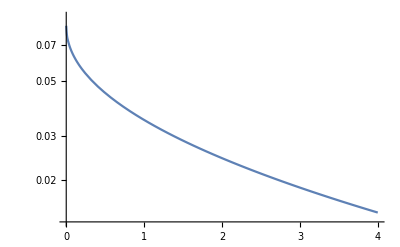

```mathematica
LogPlot[TInt[x,1],{x,0,4}]
```

```mathematica
N[√((12 Xb)/(n+2))]/.{Xb->3/10,n->4}
```

0.774597

```mathematica
ClearAll[brokenPhaseData,symPhaseData];
AbsoluteTiming[{brokenPhaseData,symPhaseData}=Module[{λ=10,n=4,maxT=1.2,ΔT=0.005,ζs={10^5,10^6,10^7,10^8,∞},tol=0.001,plotdata,pltdatasymm,ts},
ts=Table[t,{t,0.0001,maxT,ΔT}];
plotdata=ParallelTable[{t,Quiet[soln[λ,n,3/λ,ζ,1/t,tol,0.2,10000]]}//Flatten,
{ζ,ζs},{t,ts}];
pltdatasymm=ParallelTable[{t,Quiet[solnSymm[λ,n,3/λ,1/t,tol,0.2,10000]]}//Flatten,{t,ts}];
(* remove values with large imaginary parts *)
plotdata=Parallelize[Select[#,Function[v,Norm[Im[v]]<tol]]&/@plotdata];
pltdatasymm=Parallelize[Select[#,Function[v,Norm[Im[v]]<tol]]&@pltdatasymm];
{plotdata,pltdatasymm}
];
]
```

Parallelize::nopar1: (Select[#1, Function[v$, Norm[Im[v$]] < tol$2774]] &)[pltdatasymm$2774] cannot be parallelized; proceeding with sequential evaluation.

{1579.85,Null}

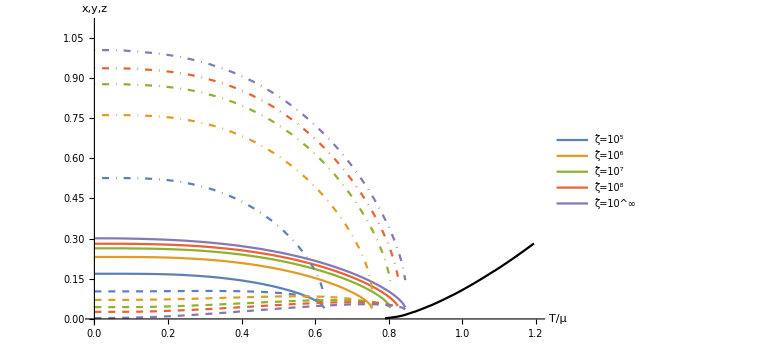

```mathematica
ssiSolns=Show[
ListLinePlot[Re@brokenPhaseData[[;;,;;,{1,2}]],PlotLegends->Table[StringTemplate["ζ̂=10^(`1`)"][If[Log[10,ζ]==DirectedInfinity[1],"∞",Log[10,ζ]]],{ζ,{10^5,10^6,10^7,10^8,∞}}],ImageSize->Large,AxesLabel->{"T/μ","x,y,z"},PlotRange->{{0,1.2},{0,1.1}},LabelStyle->Larger],
ListLinePlot[Re@brokenPhaseData[[;;,;;,{1,3}]],PlotStyle->Dashed,ImageSize->Large],
ListLinePlot[Re@brokenPhaseData[[;;,;;,{1,4}]],PlotStyle->DotDashed,ImageSize->Large],
ListLinePlot[Re@symPhaseData[[;;,{1,3}]],PlotStyle->Black,ImageSize->Large]
]
```

```mathematica
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch5", "ssi-solns.eps"}],ssiSolns]
```

C:\Users\Michael\Dropbox\PhD-thesis\images\ch5\ssi-solns.eps

```mathematica
ClearAll[TusData];
AbsoluteTiming[TusData=Module[{data,λ=10,n=4,maxT=0.9,ζs=Table[2^i,{i,14,26,0.5}],tol=0.001,t,cons},
data=(First@Last@Select[#,Function[v,Norm[Im[v]]<tol]]&/@ParallelTable[{t,Quiet[soln[λ,n,3/λ,ζ,1/t,tol,0.2,10000]]}//Flatten,{ζ,ζs},{t,0.001,maxT,tol}]);
data={ζs,data}ᵀ
];
]
```

{1475.46,Null}

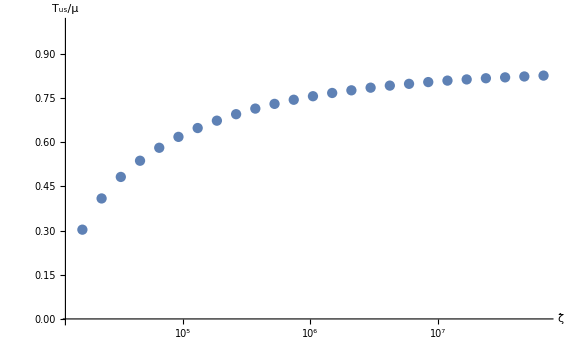

```mathematica
ssiSpinodalTemps=ListLogLinearPlot[TusData,ImageSize->Large,AxesLabel->{"ζ̂","T_us/μ"},PlotRange->{0,1},LabelStyle->Larger]
```

```mathematica
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch5","ssi-spinodal-temps.eps"}],ssiSpinodalTemps]
```

C:\Users\Michael\Dropbox\PhD-thesis\images\ch5\ssi-spinodal-temps.eps

```mathematica
Module[{λ=10,n=4,Xb=3/10,ζs={2^15,2^14,12200,10000},plt},
Table[
plt=RegionPlot[{Re@((λ/6(x-Xb)+(n-1)/6 λ(1/(16 π^2)y Log[y]+((4 x)/(ζ y))^(1/3))+λ/2 1/(16 π^2)z Log[z]+(n-1)(y^2/(2ζ x^2))^(1/3))/.z->((λ x)/3-(n-1)(y^2/(2ζ x^2))^(1/3)))>0,
Im@((λ/6(x-Xb)+(n-1)/6 λ(1/(16 π^2)y Log[y]+((4 x)/(ζ y))^(1/3))+λ/2 1/(16 π^2)z Log[z]+(n-1)(y^2/(2ζ x^2))^(1/3))/.z->((λ x)/3-(n-1)(y^2/(2ζ x^2))^(1/3)))≠0,
Re@((λ/6(x-Xb)+(n+1)/6 λ(1/(16 π^2)y Log[y]+((4 x)/(ζ y))^(1/3))+λ/6 1/(16 π^2)z Log[z])/.z->((λ x)/3-(n-1)(y^2/(2ζ x^2))^(1/3)))>y},
{x,0,.3},{y,0,.5},(*PlotLegends->{"Re[x eom]>0","Im[x eom]≠0","Re[y eom]>y"},*)FrameLabel->{x,y},PlotLabel->"ζ̂="<>ToString[ζ],PlotPoints->50,ImageSize->Large,LabelStyle->Larger];
Export[FileNameJoin[{ParentDirectory[DirectoryName[NotebookFileName[]]], "images", "ch5","ssi-hf-soln-existence-"<>ToString[ζ]<>".eps"}],plt],
{ζ,ζs}]
]
```

{C:\Users\Michael\Dropbox\PhD-thesis\images\ch5\ssi-hf-soln-existence-32768.eps,C:\Users\Michael\Dropbox\PhD-thesis\images\ch5\ssi-hf-soln-existence-16384.eps,C:\Users\Michael\Dropbox\PhD-thesis\images\ch5\ssi-hf-soln-existence-12200.eps,C:\Users\Michael\Dropbox\PhD-thesis\images\ch5\ssi-hf-soln-existence-10000.eps}